```mathematica
Directory[]
```

\\mtucifs2.iso.mtu.edu\home\

Set current directory to notebook directory

```mathematica
SetDirectory[NotebookDirectory[]]
```

H:\ELC\jan18

Import csv files

```mathematica
fn=FileNames["*.csv"]
dims=Dimensions[fn][[1]]
fn[[1]]
```

{January-22-2018.csv,January-23-2018.csv,January-24-2018.csv,January-25-2018.csv}

4

January-22-2018.csv

Number of sign-ins by day

{{11,5},{15,5},{6,5},{5,5}}

{11,15,6,5}

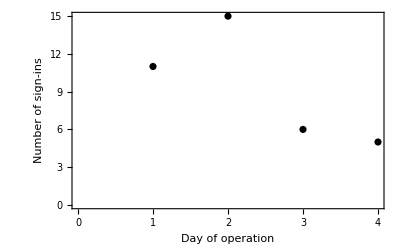

```mathematica
data=Table[Import[fn[[i]]],{i,1,dims,1}];
dimsDay=Table[Dimensions[data[[i]]],{i,1,dims}]

dimsDay[[All,1]]
ListPlot[dimsDay[[All,1]],Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"Day of operation","Number of sign-ins"},FrameStyle->Black,PlotStyle->{Black}]
```

Sign - ins by course

{5,1,5,1,1,5,5,2,5,6,2,1,4,5,1,1,1,1,4,4,1,1,1,2,7,2,3,2,4,1,1,6,3,4,1,6,2}

{{5,6},{1,14},{2,6},{6,3},{4,5},{7,1},{3,2}}

{{1,Statics},{2,MoM},{3,Dyn},{4,ETF-1},{5,MATLAB},{6,SS},{7,fdbk.}}

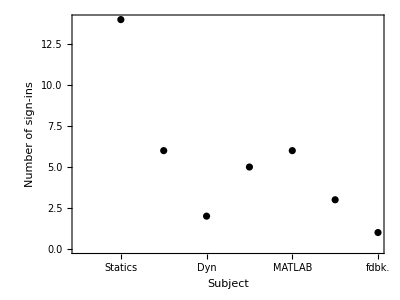

```mathematica
subjectData=Table[data[[i]][[All,1]],{i,1,dims,1}]//Flatten
tally=Tally[subjectData]
xTicks={"Statics", "Mechanics of Materials", "Dynamics", "ETF-1", "MATLAB", "Study Space", "Feedback"};
xTicks={{1,"Statics"}, {2,"MoM"}, {3,"Dyn"}, {4,"ETF-1"}, {5,"MATLAB"}, {6,"SS"}, {7,"fdbk."}}
ListPlot[tally,Frame->True,BaseStyle->{FontSize->12},FrameLabel->{"Subject","Number of sign-ins"},FrameStyle->Black,PlotStyle->{Black}
,
FrameTicks->{{Automatic,None},{xTicks,None}},AspectRatio->3/4]
```

Sign - ins by hour of day

{10,11,11,12,12,13,13,14,14,16,17,9,10,12,12,12,13,13,15,15,15,15,15,15,15,16,10,11,14,14,14,17,10,10,10,11,11}

{{10,6},{11,5},{12,5},{13,4},{14,5},{16,2},{17,2},{9,1},{15,7}}

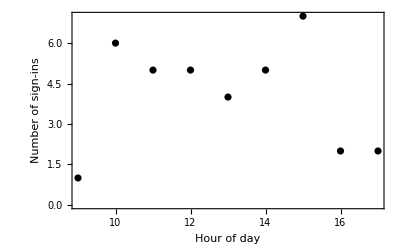

```mathematica
timeOfDay=Table[data[[i]][[All,5]],{i,1,dims,1}]//Flatten
tally=Tally[timeOfDay]
xTicks={"Statics", "Mechanics of Materials", "Dynamics", "ETF-1", "MATLAB", "Study Space", "Feedback"};
ListPlot[tally,Frame->True,BaseStyle->{FontSize->16},FrameLabel->{"Hour of day","Number of sign-ins"},FrameStyle->Black,PlotStyle->{Black}]
```